```mathematica
Needs["NDSolve`FEM`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["Ersek`RootSearch`"]
ClearAll[aux,ARR1,PLT,length,auxinDiff,plethora, pdesAdvUnif]

Here we define our set of parameters:
```

```mathematica
ourParams={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1]->0,Subscript[D, aux] ->600, Subscript[D, PLT]->540,Subscript[P, PIN]-> 0.01};

tFinal =300000;

length=400;

(*Subscript[P, PIN][x,t]:=Piecewise[{{2,0≤x≤200}},0]*)
```

```mathematica
1Eulerian coordinates
```

coordinates Eulerian

```mathematica
Testing polar transport everywhere (auxinAdvUnifTransp),only in the MZ (first peak - auxinAdvTranspOnlyMZ) or simple diffusion
```

```mathematica
arr1={D[ARR1[x,t],t]==k1 *ARR1[x,t]+ k2 *PLT[x,t]+k3*aux[x,t] -(ARR1[x,t])^3+Subscript[D, ARR1]*D[ARR1[x,t],x,x]};
plethora={D[PLT[x,t],t]==k4  *ARR1[x,t]+k5 *PLT[x,t]+k6 * aux[x,t]+Subscript[D, PLT]*D[PLT[x,t],x,x]};

(*testing polar transport everywhere (auxinAdvUnifTransp)or only in the MZ (first peak - auxinAdvTranspOnlyMZ)*)
auxinAdvUnifTransp={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+Subscript[D, aux]*D[aux[x,t],x,x]+Subscript[P, PIN]*D[aux[x,t],x]};
auxinAdvUnifTranspvary={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+Subscript[D, aux]*D[aux[x,t],x,x]+PIN*D[aux[x,t],x]}
(*auxinAdvTranspOnlyMZ={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+gamma+Subscript[D, aux]*D[aux[x,t],x,x]+Subscript[P, PIN][x,t]*D[aux[x,t],x]-0.0004};
(*)(*without auxin polar transport, only diffusion*)
(*auxinDiff={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+gamma+Subscript[D, aux]*D[aux[x,t],x,x]};*)
ic = {ARR1[x,t]==-0.1/.t->0,PLT[x,t]==-0.1/.t->0,aux[x,t]==-0.1/.t->0};
bcDiff= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==j0A/.x->length,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->length,ARR1[x,t]==-0.1/.x->0,ARR1[x,t]==-0.1/.x->length};

bcAdv= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==10/.x->length,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->length,ARR1[0,t]==+0.1, ARR1[length,t]==+0.1};


Building the set of pdes for each case

pdesDiff = {arr1,plethora,auxinDiff};
pdesAdvUnif = {arr1,plethora,auxinAdvUnifTransp};
pdesAdvUnifvary= {arr1,plethora,auxinAdvUnifTranspvary};
pdesAdvOnlyMZ = {plethora,arr1,auxinAdvTranspOnlyMZ};
```

{aux^(0,1)[x,t]==k7 ARR1[x,t]+k9 aux[x,t]+k8 PLT[x,t]+PIN aux^(1,0)[x,t]+D_aux aux^(2,0)[x,t]}

Building case each for of pdes set the

```mathematica
I case - Uniform PINs 

aux[x,t]/.x-> length/.t->tFinal/.solAdvUnif
```

aux[400,300000]/.solAdvUnif

ⅈ case-PINs Uniform

ReplaceAll::reps: {solAdvUnif} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

aux[400,300000]/.solAdvUnif

```mathematica
tFinal
```

300000

```mathematica
solAdvUnif=NDSolve[{pdesAdvUnif,ic,bcAdv}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}},PrecisionGoal->2](*Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->3,PrecisionGoal->4]
*)
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{ARR1→InterpolatingFunction[{{0., 400.}, {0., 300000.}}, <>],PLT→InterpolatingFunction[{{0., 400.}, {0., 300000.}}, <>],aux→InterpolatingFunction[{{0., 400.}, {0., 300000.}}, <>]}}

```mathematica
(**)
```

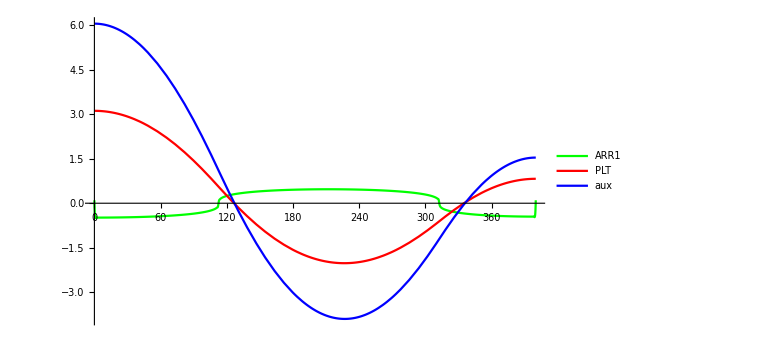

```mathematica
solveplotUnif= Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solAdvUnif[[1]]/.t->tFinal],{x,0,length},PlotRange->All,PlotLegends->{ARR1,PLT,aux},PlotStyle-> {Green,Red,Blue},(*PlotLabel->ToString[pdesAdvUnif/.Subscript[P, PIN]-> "P_PIN",TraditionalForm],BaseStyle->{FontWeight->"Bold",FontSize->12},*)ImageSize->Large]
```

```mathematica
Manipulate[Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solAdvUnif[[1]]],{x,0,length},PlotRange->All,PlotLegends->{ARR1,PLT,aux},PlotLabel->ToString[pdesAdvUnif/.Subscript[P, PIN]-> "P_PIN",TraditionalForm],BaseStyle->{FontWeight->"Bold",FontSize->6},ImageSize->Large],{t,0,tFinal}]
```

## Varying PIN permeability (robustness analysis)

```mathematica
(*PINvaryParams={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1]->0,Subscript[D, aux] ->600, Subscript[D, PLT]->540};*)
```

```mathematica
(*solvary=ParametricNDSolve[{pdesAdvUnifvary,ic,bcAdv}/.PINvaryParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal},PIN,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}},PrecisionGoal->2]*)
```

```mathematica
(*fun=aux/.ParametricNDSolve[{pdesAdvUnifvary,ic,bcAdv}/.PINvaryParams/.alpha-> 0/.beta-> 0/.gamma->0,aux,{x,0,length},{t,0,tFinal},PIN,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}},PrecisionGoal->2]*)
```

```mathematica
(**)
```

```mathematica
(*Table[i,{i,0.01,1*10^-1,0.01}]*)
```

```mathematica
(**)
```

```mathematica
(*Plot[Evaluate@Table[fun[PIN][x,t]/.t-> tFinal,{PIN,0.01,1*10^-1,0.01}],{x,0,length},PlotLegends->Table[Row[{"P_PIN = ",i}],{i,0.01,1*10^-1,0.01}]]
Table[PIN,{PIN,0.01,1*10^-1,0.01}]*)
```

```mathematica
(*Grid[Join[{{"t","Varying δ","Varying k_aux","Varying D_aux","Varying P_PIN"}},
Table[{StringJoin["t = ",ToString[τ]],
Plot[Evaluate@Table[δDparfun[δ,d/.{d->600,Subscript[P, PIN]-> 5},Subscript[P, PIN]/.{d->600,Subscript[P, PIN]-> 5},Subscript[k, aux]/.Subscript[k, aux]-> 1.97*10^-3][x,τ],{δ,{10^-2,10^-1,1,100}}],{x,0,length/.parδDPINparams},ImageSize-> Medium,PlotRange->All,PlotLegends->Table[Row[{"δ_aux = ",i}],{i,{10^-7,10^-6,10^-5,10^-3}}]],Plot[Evaluate@Table[δDparfun[δ,d/.{d->600,Subscript[P, PIN]-> 5},Subscript[P, PIN]/.{d->600,Subscript[P, PIN]-> 5},Subscript[k, aux]][x,τ],{Subscript[k, aux],{10^-6,1.97*10^-3,10^-4}}],{x,0,length/.parδDPINparams},PlotLegends->Table[Row[{"k_aux = ",i}],{i,{10^-6,1.97*10^-3,10^-4}}]],Plot[Evaluate@Table[δDparfun[δ/.{δ->5.83*10^-1,Subscript[P, PIN]-> 5},d,Subscript[P, PIN]/.{δ->5.83*10^-1,Subscript[P, PIN]-> 5},Subscript[k, aux]/.Subscript[k, aux]-> 1.97*10^-3][x,τ],{d,200,600,200}],{x,0,length/.parδDPINparams},ImageSize-> Medium,PlotRange->All,PlotLegends->Table[Row[{"D_aux = ",i}],{i,200,600,200}]],
Plot[Evaluate@Table[δDparfun[δ/.{δ->5.83*10^-1,d->600},d/.{δ->5.83*10^-1,d->600},Subscript[P, PIN],Subscript[k, aux]/.Subscript[k, aux]-> 1.97*10^-3][x,τ],{Subscript[P, PIN],2,10,4}],{x,0,length/.parδDPINparams},ImageSize-> Medium,PlotRange->All,PlotLegends->Table[Row[{"P_PIN = ",i}],{i,2,10,4}]]},{τ,{0,100,1000,10000}}]]]*)
```

```mathematica
(*II case - PINs in MZ only*)
```

```mathematica
(*solveAdvOnlyMZ=NDSolve[{pdesAdvOnlyMZ,ic,bcAdv}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->300}},PrecisionGoal->2];*)
```

```mathematica
(*solveplotonlyMZ= Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solveAdvOnlyMZ[[1]]/.t->tFinal],{x,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},PlotLabel->ToString[pdesAdvOnlyMZ/.Subscript[P, PIN][x,t]-> "P_PIN[x,t]",TraditionalForm],BaseStyle->{FontWeight->"Bold",FontSize->6},ImageSize->Large]*)
```

```mathematica
(**)
```

```mathematica
(**)
```

#### III case - diffusion only

```mathematica
(*solveDiff=NDSolve[{pdesDiff,ic,bcDiff}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->300}} ,PrecisionGoal->2]*)
```

```mathematica
(*solveplotDiff= Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solveDiff[[1]]/.t->tFinal],{x,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},PlotLabel->ToString[pdesDiff,TraditionalForm],BaseStyle->{FontWeight->"Bold",FontSize->7},ImageSize->Large]*)
```

```mathematica
(*Including the resulting steady state pattern as initial condition on a longer domain - the initial condition will be the obtained interpolating function for a portion of the domain (equal to the previous length) and a small perturbation (+/- 0.1) for the remaining part of the NewLength:*)
```

```mathematica
(*NewLength=800;*)
```

```mathematica
(**)
```

```mathematica
(*ic1old=Evaluate[ARR1/.solAdvUnif[[1,1]]/.t->tFinal];
ic2old=Evaluate[PLT/.solAdvUnif[[1,2]]/.t->tFinal];
ic3old=Evaluate[aux/.solAdvUnif[[1,3]]/.t->tFinal];

initialcondleftARR1[x]:=If[0≤x<=length,ic1old[x,tFinal],-0.1]
initialcondleftPLT[x]:=If[0≤x<=length,ic2old[x,tFinal],-0.1]
initialcondleftaux[x]:=If[0≤x<=length,ic3old[x,tFinal],-0.1]

initialcondrightARR1[x]:=If[NewLength-length≤x≤NewLength,ic1old[x,tFinal],-0.1]
initialcondrightPLT[x]:=If[NewLength-length≤x≤NewLength,ic2old[x,tFinal],-0.1]
initialcondrightaux[x]:=If[NewLength-length≤x≤NewLength,ic3old[x,tFinal],-0.1]



icNewLengthleft = {ARR1[x,t]==initialcondleftARR1[x]/.t->0,PLT[x,t]==initialcondleftPLT[x]/.t->0,aux[x,t]==initialcondleftaux[x]/.t->0}

icNewLengthright = {ARR1[x,t]==initialcondrightARR1[x]/.t->0,PLT[x,t]==initialcondrightPLT[x]/.t->0,aux[x,t]==initialcondrightaux[x]/.t->0}

bcNewLength= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==j0A/.x->NewLength/.j0A -> 10^-3/.Subscript[P, PIN]-> 0.1,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->NewLength,ARR1[x,t]==-0.1/.x->0,ARR1[x,t]==0.1/.x->NewLength};

NewInCondleftPlot= Plot[{icNewLengthleft[[1,2]],icNewLengthleft[[2,2]],icNewLengthleft[[3,2]]}/.t->0,{x,0,NewLength},PlotRange-> All]
NewInCondrightPlot= Plot[{icNewLengthright[[1,2]],icNewLengthright[[2,2]],icNewLengthright[[3,2]]}/.t->0,{x,0,NewLength}];
*)
```

```mathematica
(*NewInCondleftPlotLag= Plot[{icNewLengthleftLag[[1,2]],icNewLengthleftLag[[2,2]],icNewLengthleftLag[[3,2]]}/.t->0,{X,0,NewLength},PlotRange-> All]

*)
```

```mathematica
(*Plot[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,{x,0,length}]*)
```

```mathematica
(*Solving the equations on a longer domain - no growth, no lagrangian coordinates 
solveNewLengthleft=NDSolve[{pdesAdvUnif,icNewLengthleft,bcNewLength}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,NewLength},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->20}},PrecisionGoal->2]
solveplotNewLengthleft= Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solveNewLengthleft⟦1⟧/.t->tFinal],{x,0,NewLength},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large]
*)
```

Here I want to find where the local maxima  and minima of the PLT function. In order to do that, I need to have the first derivative ==0:

```mathematica
allrootsPLT= Flatten@RootSearch[D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x]==0,{x,-0.5,length+100}]
```

InterpolatingFunction::dmval: Input value {-0.5,300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {401.241,300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {402.906,300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{x→2.62376×10^-6,x→226.475,x→400.}

```mathematica
allrootsaux= Flatten@RootSearch[D[aux[x,tFinal]/.solAdvUnif⟦1,3⟧,x]==0,{x,-0.5,length+100}]
```

InterpolatingFunction::dmval: Input value {-0.5,300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {401.241,300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {402.906,300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{x→5.4684×10^-6,x→226.828,x→400.}

```mathematica
Now I study the sign of the second derivative for the found x values. If the second derivative is<0, that point is a maximum ( the function is concave down) if >0 ,is a minimum ( the function is concave up). If  PLT'' ==0, the point is called inflection point ( at the intersection with the axis), and here the function changes concavity. The next command evaluates this numerically:
```

```mathematica
PLTinters=MapThread[#->Which[#2<0,"max",#2>0,"min",True,"inflection"]&,{x/.allrootsPLT,D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x,x]/.allrootsPLT}]
```

MapThread::mptd: Object 2.62376×10^-6 at position {2, 1} in MapThread[#1→Which[#2<0,max,#2>0,min,True,inflection]&,{2.62376×10^-6,-0.00043111}] has only 0 of required 1 dimensions.

MapThread[#1→Which[#2<0,max,#2>0,min,True,inflection]&,{2.62376×10^-6,-0.00043111}]

```mathematica
PLTaxislocalmax=DeleteCases[Table[If[D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x,x]<0/.allrootsPLT⟦i⟧,allrootsPLT⟦i⟧],{i,1,Length[allrootsPLT]}], Null]
```

{x→2.62376×10^-6,x→400.}

```mathematica
PLTaxislocalmin= DeleteCases[Table[If[D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x,x]>0/.allrootsPLT⟦i⟧,allrootsPLT⟦i⟧],{i,1,Length[allrootsPLT]}], Null]
```

{x→226.475}

```mathematica
auxinmin=x/.allrootsaux[[2]]
```

226.828

```mathematica
ARR1roots=RootSearch[Evaluate[ARR1[x,tFinal]/.solAdvUnif⟦1,1⟧]==0,{x,0,length}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{{x→0.0639665},{x→112.486},{x→312.561},{x→399.932}}

```mathematica
ARR1axislocalmax=DeleteCases[Table[If[D[ARR1[x,tFinal]/.solAdvUnif⟦1,1⟧,x,x]<0/.ARR1roots⟦i⟧,ARR1roots⟦i⟧],{i,1,Length[ARR1roots]}], Null]
```

{{x→112.486}}

```mathematica
ARR1left=x/.ARR1roots[[2]]
```

112.486

```mathematica
ARR1right=x/.ARR1roots[[3]]
```

312.561

```mathematica
inflectionpoints=RootSearch[D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x,x]==0,{x,0,length}];
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

#### The red dots in the plot show all the local maxima

```mathematica
Plot[{PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x]},{x,0,length},Epilog->{AbsolutePointSize@5,Red,Point[{#,PLT[#,tFinal]/.solAdvUnif⟦1,2⟧}&/@(x/.PLTaxislocalmax)]}]
```

General::ivar: 0.00817143 is not a valid variable.

General::ivar: 8.17144 is not a valid variable.

General::ivar: 16.3347 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

General::ivar: 0.00817143 is not a valid variable.

General::ivar: 8.17144 is not a valid variable.

General::ivar: 16.3347 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

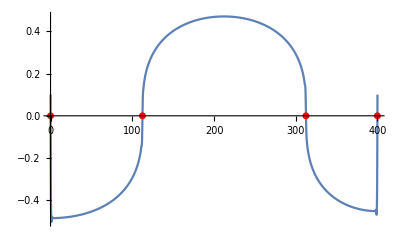

```mathematica
Plot[{ARR1[x,tFinal]/.solAdvUnif⟦1,1⟧,D[ARR1[x,tFinal]/.solAdvUnif⟦1,1⟧,x,x]},{x,0,length},Epilog->{AbsolutePointSize@5,Red,Point[{#,ARR1[#,tFinal]/.solAdvUnif⟦1,1⟧}&/@(x/.ARR1roots)]}]
```

```mathematica
PLTaxismaxint=Table[PLTaxislocalmax[[i]],{i,1,2}]
```

{x→2.62376×10^-6,x→400.}

```mathematica
PLTmaxima=Sort[Table[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧/.PLTaxismaxint[[i]],{i,1, Length[PLTaxismaxint]}], Greater]
```

{3.11505,0.823534}

```mathematica
PLTminima= PLT[x,tFinal]/.solAdvUnif⟦1,2⟧/.PLTaxislocalmin
```

-2.02152

```mathematica
PLTxmaxima=Table[Sort[DeleteCases[Table[If[D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x,x]<0/.allrootsPLT⟦i⟧,x/.allrootsPLT⟦i⟧],{i,1,Length[allrootsPLT]}], Null],Smaller][[j]],{j,1,2}]
```

{2.62376×10^-6,400.}

```mathematica
Total[PLTxmaxima]
```

400.

```mathematica
PLTxminima=Sort[DeleteCases[Table[If[D[PLT[x,tFinal]/.solAdvUnif⟦1,2⟧,x,x]>0/.allrootsPLT⟦i⟧,x/.allrootsPLT⟦i⟧],{i,1,Length[allrootsPLT]}], Null],Smaller]
```

{226.475}

```mathematica
rightboundfirstpeak=x/.inflectionpoints[[1]]
```

112.486

```mathematica
inters=X/.Sequence @@NSolve[Evaluate[{PLT[X,t]}/.solAdvUnif⟦1,2⟧/.t->tFinal]==PLTmaxima⟦2⟧,X]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

105.989

```mathematica
tolerance=(PLTmaxima[[1]]-PLTmaxima[[2]])/4
```

0.572879

```mathematica
(*newPLTlimit=PLTmaxima[[2]]+tolerance*)
```

```mathematica
newPLTlimit=PLTmaxima[[1]]-tolerance
```

2.54217

```mathematica
intersPLTmaxima=X/.RootSearch[Evaluate[PLT[X,tFinal]/.solAdvUnif⟦1,2⟧]==newPLTlimit,{X,0,length}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{51.8356}

```mathematica
intersection=X/.RootSearch[Evaluate[PLT[X,tFinal]/.solAdvUnif⟦1,2⟧]==0,{X,0,length}]
```

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

{126.487,334.865}

```mathematica
data=Flatten@{xmaxima,intersection}
```

{xmaxima,126.487,334.865}

```mathematica
clusters=FindClusters[data]
```

FindClusters::amtd: FindClusters is unable to automatically select an appropriate dissimilarity function for the input data {xmaxima,126.487,334.865}.

FindClusters[{xmaxima,126.487,334.865}]

```mathematica
sortedclus=Table[Sort[clusters[[i]]],{i,1,Length[clusters]}]
```

{{126.487,334.865,xmaxima}}

```mathematica
clusters[[2,1]]
```

Part::partw: Part 2 of FindClusters[{xmaxima,126.487,334.865}] does not exist.

FindClusters[{xmaxima,126.487,334.865}]⟦2,1⟧

```mathematica
(*plotclust=Show[Plot[Evaluate[{PLT[X,t]}/.solAdvUnif⟦1,2⟧/.t->tFinal], {X,0,length}],Plot[Evaluate[PLT[X,t]/.solAdvUnif⟦1,2⟧/.t->tFinal] , {X,sortedclus⟦1,1⟧, sortedclus⟦1,Length[sortedclus⟦1⟧]⟧},Filling-> Axis ],Plot[Evaluate[PLT[X,t]/.solAdvUnif⟦1,2⟧/.t->tFinal] , {X,sortedclus[[2,1]], sortedclus[[2,Length[sortedclus⟦2⟧]]]},Filling-> Axis ],Plot[Evaluate[PLT[X,t]/.solAdvUnif⟦1,2⟧/.t->tFinal] , {X,sortedclus[[3,1]], sortedclus[[3,Length[sortedclus⟦3⟧]]]},Filling-> Axis ]];*)
```

```mathematica
Evaluate[PLT[intersPLTmaxima[[1]],tFinal]/.solAdvUnif[[1,2]]]
```

2.54217

```mathematica
regionsofint=FindClusters[Table[If[Evaluate[PLT[intersPLTmaxima[[i]],tFinal]/.solAdvUnif[[1,2]]]> PLTmaxima[[2]],intersPLTmaxima[[i]]],{i,1,Length[intersPLTmaxima]}]]
```

{{51.8356}}

```mathematica
regionsofint⟦1,Length[regionsofint⟦1⟧]⟧
```

51.8356

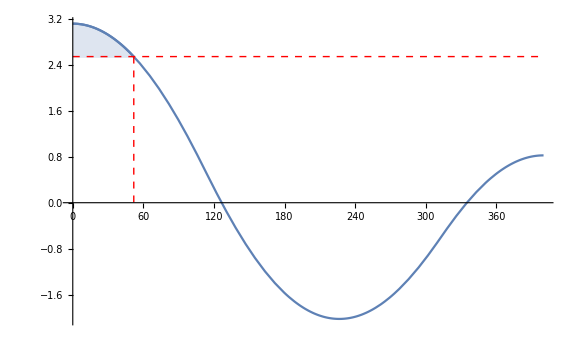

```mathematica
Show[Plot[Evaluate[{PLT[X,t]}/.solAdvUnif⟦1,2⟧/.t->tFinal],{X,0,length},ImageSize-> Large, Epilog->{Red, Dashed,Line[{{0,newPLTlimit},{length,newPLTlimit}}],Red, Dashed,Table[Line[{{intersPLTmaxima[[i]],newPLTlimit},{intersPLTmaxima[[i]],0}}],{i,1,Length[intersPLTmaxima]}]}],
Plot[Evaluate[PLT[X,t]/.solAdvUnif⟦1,2⟧/.t->tFinal] , {X,0, regionsofint⟦1,Length[regionsofint⟦1⟧]⟧},Filling-> Axis ]]
```

```mathematica
(*xval=Table[i,{i,1,500,0.1}];*)
```

```mathematica
(*imppos=Position[{Table[Evaluate[PLT[XVal,tFinal]/.solAdvUnif⟦1,2⟧],{XVal,1,500}]},_?(#>PLTmaxima[[2]]&)]*)
```

```mathematica
(*pltvalues=Extract[{Table[Evaluate[PLT[XVal,tFinal]/.solAdvUnif⟦1,2⟧],{XVal,1,500}]},imppos]
*)
```

```mathematica
(*onlyimpvalue=Table[imppos[[i,2]],{i,1,Length[imppos]}]*)
```

```mathematica
(*data2=Flatten@{xmaxima,onlyimpvalue}
*)
```

```mathematica
(*newclust=FindClusters[data2]*)
```

```mathematica
(*newsortedclus=Table[Sort[newclust[[i]]],{i,1,Length[newclust]}]*)
```

```mathematica
(*Length[onlyimpvalue]*)
```

```mathematica
(*Show[Plot[Evaluate[{PLT[X,t]}/.solAdvUnif⟦1,2⟧/.t->tFinal],{X,0,length},ImageSize-> Large, Epilog->{Red, Dashed,Line[{{0,newPLTlimit},{length,newPLTlimit}}],Red, Dashed,Table[Line[{{intersPLTmaxima[[i]],PLTmaxima⟦2⟧},{intersPLTmaxima[[i]],0}}],{i,1,Length[intersPLTmaxima]}]}],
Plot[Evaluate[PLT[X,t]/.solAdvUnif⟦1,2⟧/.t->tFinal] , {X,onlyimpvalue⟦1⟧,Length[onlyimpvalue]},Filling->Axis]]*)
```

```mathematica
Clear[γonlyMZPLT]
```

```mathematica
(*γonlyMZPLT:=0.0006-0.0006/(1+Exp[-(X)]*10^34)*)
```

#### Now I have to define my growth rate as a step function that has a fixed value only in the region of the first peak (between 0 and rightboundfirstpeak, and 0 otherwise. However, a step or piecewise function in not differentiable when I solve my PDEs, so I need continuous function that shows the same behaviour:

```mathematica
(*γonlyMZPLT:=Rationalize[0.000006+0.000006/(1+Exp[-(PLT[X,t]-newPLTlimit)*10])](*(0.02*10^-3)/(1+Exp[-0.025X]*1000)*)*)
growthPLT:=10^-7
basalgrowth:=10^-6
(*γonlyMZPLT=Piecewise[{{0.000001,PLT[X,t]>newPLTlimit && 0≤ X≤  intersection[[1]]},{0.00001 , ARR1left≤X≤ ARR1right}}]

Apply[(If[#2===what,"yay",If[#2===whoops,"nay"]])&,{-5,what}]
Apply[(If[#2===what,"yay",If[#2===whoops,"nay"]])&,{-5,whoops}]
(*"yay" "nay"*)*)
```

This is the growth rate that takes into account PLT growth, ARR1 growth or null otherwise :

```mathematica
γonlyMZPLT:=Piecewise[{{growthPLT,PLT[X,t]≥ newPLTlimit&&PLTxmaxima⟦1⟧≤ X≤  auxinmin},{basalgrowth,PLT[X,t]≤0&&(ARR1left≤X≤ ARR1right)}}]
```

```mathematica
(*Apply[(If[#2==2,"yay",If[#2==3,"nay"]])&,{-5,3}]
nay*)
```

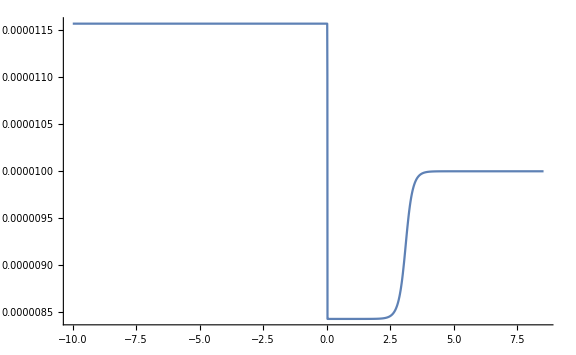

```mathematica
Plot[10^-6 ArcTan[Sin[0.3*PLT[X,t]-3.15]/Exp[30*(PLT[X,t]-3.15)*0.2]]+10^-5,{PLT[X,t],-10,newPLTlimit+6},ImageSize->Large]
```

```mathematica
Lagrangian coordinates - solving the system with growth

(*Assuming uniform growth within the MZ (γ3 is the growth rate, [1/s]) 
*)
(*γ3:=If[0≤ X≤ 200,0.000004,0]


Plot[Evaluate[γ3],{X,0,500},PlotRange->All]

Plot[Evaluate[Γ[X,t]/.t->1000],{X,0,500},PlotRange->All]
*)
```

coordinates Lagrangian-growth solving system the with

```mathematica
Rearranging spatial terms using Lagrangian coordinates (for growing domains)
```

coordinates domains for growing Lagrangian Rearranging spatial terms using

```mathematica
Clear [Γ]
```

```mathematica
Γ[X,t]:= X
```

```mathematica
SpatialTermsLagAdvUnif={Subscript[D, aux]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[aux[X,t],X]+1/D[Γ[X,t],X]^2 D[aux[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]+Subscript[P, PIN]*(1/D[Γ[X,t],X] D[aux[X,t],X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]};
SpatialTermsLagAdvOnlyMZ={Subscript[D, aux]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[aux[X,t],X]+1/D[Γ[X,t],X]^2 D[aux[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]+Subscript[P, PIN][X,t]*(1/D[Γ[X,t],X] D[aux[X,t],X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]};
SpatialTermsLagOnlyDiff={Subscript[D, aux]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[aux[X,t],X]+1/D[Γ[X,t],X]^2 D[aux[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]};
```

```mathematica
Writing pdes substituting spatial terms in Lagragian notation
```

in Lagragian notation pdes spatial substituting terms Writing

```mathematica
arr1Lag={D[ARR1[X,t],t]==k1 *ARR1[X,t]+ k2 *PLT[X,t]+k3*aux[X,t] +alpha-(ARR1[X,t])^3+Subscript[D, ARR1]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[ARR1[X,t],X]+1/D[Γ[X,t],X]^2 D[ARR1[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*ARR1[X,t]};
plethoraLag={D[PLT[X,t],t]==k4  *ARR1[X,t]+k5 *PLT[X,t]+k6 * aux[X,t]+ beta+Subscript[D, PLT]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[PLT[X,t],X]+1/D[Γ[X,t],X]^2 D[PLT[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*PLT[X,t]};

auxinAdvUnifTranspLag={D[aux[X,t],t]==k7 *ARR1[X,t] +k8 *PLT[X,t]+k9  * aux[X,t]+gamma+Subscript[D, aux]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[aux[X,t],X]+1/D[Γ[X,t],X]^2 D[aux[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]+Subscript[P, PIN]*(1/D[Γ[X,t],X] D[aux[X,t],X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]};
(*auxinAdvTranspOnlyMZLag={D[aux[X,t],t]==k7 *ARR1[X,t] +k8 *PLT[X,t]+k9  * aux[X,t]+gamma+Subscript[D, aux]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3D[aux[X,t],X]+1/D[Γ[X,t],X]^2 D[aux[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]+Subscript[P, PIN][X,t]*(1/D[Γ[X,t],X] D[aux[X,t],X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]};
(*without auxin polar transport, only diffusion)*)
auxinDiffLag={D[aux[X,t],t]==k7 *ARR1[X,t] +k8 *PLT[X,t]+k9  * aux[X,t]+gamma+Subscript[D, aux]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3D[aux[X,t],X]+1/D[Γ[X,t],X]^2 D[aux[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]};*)

icLag = {ARR1[X,t]==-0.1/.t->0,PLT[X,t]==-0.1/.t->0,aux[X,t]==-0.1/.t->0};
bcAdvLag= {D[aux[X,t],X]==0/.X->0,D[aux[X,t],X]==j0A/.X->length/.j0A -> 10^-3,D[PLT[X,t],X]==0/.X->0,D[PLT[X,t],X]==0/.X->length,(*PLT[X,t]==0/.X->0,PLT[X,t]==0/.X->initLength,*)ARR1[0,t]==-0.1, ARR1[length,t]==-0.1};


bcDiffLag= {D[aux[X,t],X]==0/.X->0,D[aux[X,t],X]==0/.X->initLength/.j0A -> 10^-3,(*D[PLT[X,t],X]==0/.X->0,D[PLT[X,t],X]==0/.X->initLength,*)PLT[X,t]==0/.X->0,PLT[X,t]==0/.X->initLength,ARR1[0,t]==0, ARR1[initLength,t]==0};
```

```mathematica
Now solving the same equations including growth only in the region of the first peak-growth depends on PLT concentration as set in the previous section
I case-PIN uniform
```

-as concentration depends growth in on PLT previous section set the+equations first growth in including of only peak region same solving the^3 Mon 3 Jul 2017 11:19:48GMT+2.

ⅈ case-PIN uniform

```mathematica
Building the set of pdes for each case
```

Building case each for of pdes set the

```mathematica
pdesDiffnoGrowth= {plethoraLag,arr1Lag,auxinDiffLag}/.γonlyMZPLT-> 0;
pdesAdvUnifnoGrowth= {plethoraLag/.γonlyMZPLT-> 0,arr1Lag/.γonlyMZPLT-> 0,auxinAdvUnifTranspLag/.γonlyMZPLT-> 0};
pdesAdvOnlyMZnoGrowth = {plethoraLag,arr1Lag,auxinAdvTranspOnlyMZLag}/.γonlyMZPLT-> 0;
```

```mathematica
First solving equations without growth (with uniform PINs,with PINs only in the meristem,with diffusion only)
I case-uniform PINs:
```

```mathematica
tFinal=200000;
```

```mathematica
solLagAdvUnifnogrowth=NDSolve[{pdesAdvUnifnoGrowth,icLag,bcAdvLag} /.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{X,0,length},{t,0,tFinal},(*Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}}*)(*Method->"StiffnessSwitching",AccuracyGoal->5,PrecisionGoal->3]*)Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}},PrecisionGoal->2]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{ARR1→InterpolatingFunction[{{0., 400.}, {0., 200000.}}, <>],PLT→InterpolatingFunction[{{0., 400.}, {0., 200000.}}, <>],aux→InterpolatingFunction[{{0., 400.}, {0., 200000.}}, <>]}}

```mathematica
(**)
```

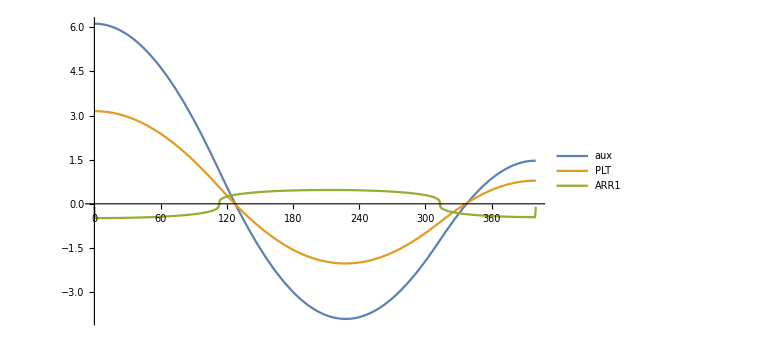

```mathematica
solveplotLagUnif= Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvUnifnogrowth[[1]]/.t->tFinal],{X,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large]
```

```mathematica
(*
*)
```

```mathematica
(*pdesAdvUnifnoGrowth*)
```

```mathematica
(*turingnogrowth=Manipulate[Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvUnifnogrowth[[1]]],{X,0,length},PlotRange->All,ImageSize->Large],{t,0,1000000}]*)
```

```mathematica
(*Export["turingnogrowth.avi",turingnogrowth, "FrameRate"->3]


SystemOpen["turingnogrowth.avi"]*)
```

```mathematica
(*II case- PINs only in MZ

solLagAdvOnlyMZnoGrowth=NDSolve[{pdesAdvOnlyMZnoGrowth ,icLag,bcAdvLag}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{X,0,initLength},{t,0,tFinal},{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200}},PrecisionGoal->2](*{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->5,"DifferenceOrder"->Pseudospectral}}, PrecisionGoal->2]*);

case II-in MZ only PINs


solveplotOnlyMZLagnoGrowth= Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvOnlyMZnoGrowth[[1]]/.t->tFinal],{X,0,initLength},PlotRange->All,PlotLabel->ToString[pdesAdvUnifnoGrowth/.Subscript[P, PIN][X,t]-> "P_PIN[X,t]"/.Γ[X,t]->"Γ[X,t]"/.D[Γ[X,t],X,X]->"Γ[X,t]^(2, 0)"/.D[Γ[X,t],X]->"Γ[X,t]^(1, 0)"/.D[Γ[X,t],X,t]->"Γ[X,t]^(1, 1)"/.γ3-> "γ3",TraditionalForm],BaseStyle->{FontWeight->"Bold",FontSize->5},PlotLegends->{aux,PLT,ARR1},ImageSize->Large]*)
```

```mathematica
(*III case - only diffusion
case III-diffusion only
solLagDiffnoGrowth=NDSolve[{pdesDiffnoGrowth ,icLag,bcAdvLag}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{X,0,initLength},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->10,"DifferenceOrder"->Pseudospectral}}, PrecisionGoal->1]



solveplotOnlyDiffnoGrowth= Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagDiffnoGrowth[[1]]/.t->tFinal],{X,0,initLength},PlotRange->All,PlotLabel->ToString[pdesAdvUnifnoGrowth/.Subscript[P, PIN]-> "P_PIN"/.Γ[X,t]->"Γ[X,t]"/.D[Γ[X,t],X,X]->"Γ[X,t]^(2, 0)"/.D[Γ[X,t],X]->"Γ[X,t]^(1, 0)"/.D[Γ[X,t],X,t]->"Γ[X,t]^(1, 1)"/.γ3-> "γ3",TraditionalForm],BaseStyle->{FontWeight->"Bold",FontSize->5},PlotLegends->{aux,PLT,ARR1},ImageSize->Large]*)
```

```mathematica
(*Solving the equations on a longer domain - no growth, lagrangian coordinates 

solveAdvNewLengthleft=NDSolve[{pdesAdvUnifLag,icNewLengthleftLag ,}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{X,0,length},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->20}},PrecisionGoal->2]

solveplotNewLengthleft= Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solveNewLengthleft⟦1⟧/.t->tFinal],{x,0,NewLength},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large]
*)
```

```mathematica
Solving the equations on a longer domain - growth, lagrangian coordinates
```

{ARR1[X,0]==InterpolatingFunction[{{0., 400.}, {0., 200000.}}, <>][X,200000],PLT[X,0]==InterpolatingFunction[{{0., 400.}, {0., 200000.}}, <>][X,200000],aux[X,0]==InterpolatingFunction[{{0., 400.}, {0., 200000.}}, <>][X,200000]}

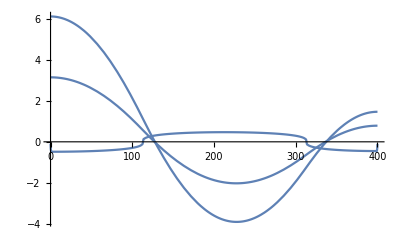

ⅇ^(t (Piecewise[{{1/10000000, PLT[X,t]≥2.54217&&2.62376×10^-6≤X≤226.828}, {1/1000000, PLT[X,t]≤0&&112.486≤X≤312.561}, {0, True}}])) X

ⅇ^(t γPLTARR1) X

```mathematica
(*NewLength=700;*)
ic1oldLag=Evaluate[ARR1/.solLagAdvUnifnogrowth[[1,1]]/.t->tFinal];
ic2oldLag=Evaluate[PLT/.solLagAdvUnifnogrowth[[1,2]]/.t->tFinal];
ic3oldLag=Evaluate[aux/.solLagAdvUnifnogrowth[[1,3]]/.t->tFinal];

initialcondleftARR1Lag[X]:=ic1oldLag[X,tFinal]
initialcondleftPLTLag[X]:=ic2oldLag[X,tFinal]
initialcondleftauxLag[X]:=ic3oldLag[X,tFinal]


icNewLengthleftLag = {ARR1[X,t]==initialcondleftARR1Lag[X]/.t->0,PLT[X,t]==initialcondleftPLTLag[X]/.t->0,aux[X,t]==initialcondleftauxLag[X]/.t->0}

Plot[{icNewLengthleftLag [[1,2]],icNewLengthleftLag [[2,2]],icNewLengthleftLag [[3,2]]}/.t->0,{X,0,length},PlotRange-> All]

Clear[Γ]
Γ[X,t]=∫_0^X (Exp[∫_0^t (γonlyMZPLT)ⅆτ])ⅆz
Γ1[X,t]=∫_0^X (Exp[∫_0^t (γPLTARR1)ⅆτ])ⅆz
(*
Γ[X,t]:= X*(1+γonlyMZPLT*t)*)
arr1Lag={D[ARR1[X,t],t]==k1 *ARR1[X,t]+ k2 *PLT[X,t]+k3*aux[X,t] +alpha-(ARR1[X,t])^3+Subscript[D, ARR1]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[ARR1[X,t],X]+1/D[Γ[X,t],X]^2 D[ARR1[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*ARR1[X,t]};
plethoraLag={D[PLT[X,t],t]==k4  *ARR1[X,t]+k5 *PLT[X,t]+k6 * aux[X,t]+ beta+Subscript[D, PLT]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[PLT[X,t],X]+1/D[Γ[X,t],X]^2 D[PLT[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*PLT[X,t]};

auxinAdvUnifTranspLag={D[aux[X,t],t]==k7 *ARR1[X,t] +k8 *PLT[X,t]+k9  * aux[X,t]+gamma+Subscript[D, aux]*(-D[Γ[X,t],X,X]/D[Γ[X,t],X]^3 D[aux[X,t],X]+1/D[Γ[X,t],X]^2 D[aux[X,t],X,X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]+Subscript[P, PIN]*(1/D[Γ[X,t],X] D[aux[X,t],X])-D[Γ[X,t],X,t]/D[Γ[X,t],X]*aux[X,t]};

icLag = {ARR1[X,t]==-0.1/.t->0,PLT[X,t]==-0.1/.t->0,aux[X,t]==-0.1/.t->0};
bcAdvLag= {D[aux[X,t],X]==0/.X->0,D[aux[X,t],X]==j0A/.X->length/.j0A -> 10^-3,D[PLT[X,t],X]==0/.X->0,D[PLT[X,t],X]==0/.X->length,(*PLT[X,t]==0/.X->0,PLT[X,t]==0/.X->initLength,*)ARR1[0,t]==-0.1, ARR1[length,t]==-0.1};



pdesAdvUnifGrowth = {plethoraLag,arr1Lag,auxinAdvUnifTranspLag};
```

```mathematica
(*arr1Lag1={D[ARR1[X,t],t]==k1 *ARR1[X,t]+ k2 *PLT[X,t]+k3*aux[X,t] +alpha-(ARR1[X,t])^3+Subscript[D, ARR1]*(-D[Γ1[X,t],X,X]/D[Γ1[X,t],X]^3D[ARR1[X,t],X]+1/D[Γ1[X,t],X]^2 D[ARR1[X,t],X,X])-D[Γ1[X,t],X,t]/D[Γ1[X,t],X]*ARR1[X,t]};
plethoraLag1={D[PLT[X,t],t]==k4  *ARR1[X,t]+k5 *PLT[X,t]+k6 * aux[X,t]+ beta+Subscript[D, PLT]*(-D[Γ1[X,t],X,X]/D[Γ1[X,t],X]^3D[PLT[X,t],X]+1/D[Γ1[X,t],X]^2 D[PLT[X,t],X,X])-D[Γ1[X,t],X,t]/D[Γ1[X,t],X]*PLT[X,t]};

auxinAdvUnifTranspLag1={D[aux[X,t],t]==k7 *ARR1[X,t] +k8 *PLT[X,t]+k9  * aux[X,t]+gamma+Subscript[D, aux]*(-D[Γ1[X,t],X,X]/D[Γ1[X,t],X]^3D[aux[X,t],X]+1/D[Γ1[X,t],X]^2 D[aux[X,t],X,X])-D[Γ1[X,t],X,t]/D[Γ1[X,t],X]*aux[X,t]+Subscript[P, PIN]*(1/D[Γ1[X,t],X] D[aux[X,t],X])-D[Γ1[X,t],X,t]/D[Γ1[X,t],X]*aux[X,t]};

icLag = {ARR1[X,t]==-0.1/.t->0,PLT[X,t]==-0.1/.t->0,aux[X,t]==-0.1/.t->0};
bcAdvLag= {D[aux[X,t],X]==0/.X->0,D[aux[X,t],X]==j0A/.X->length/.j0A -> 10^-3,D[PLT[X,t],X]==0/.X->0,D[PLT[X,t],X]==0/.X->length,(*PLT[X,t]==0/.X->0,PLT[X,t]==0/.X->initLength,*)ARR1[0,t]==-0.1, ARR1[length,t]==-0.1};

pdesAdvUnifGrowth1 = {plethoraLag1,arr1Lag1,auxinAdvUnifTranspLag1};*)
```

```mathematica
tFinal=170000
```

170000

```mathematica
(*Manipulate[Plot[ⅇ^(t If[PLT[X,t]>7.7132382700888895,6.*^-6,6.*^-10]) X,{X,0,40}],{t,0,100},{y,-10,50}]*)
```

```mathematica
(*solLagAdvUnifGrowthARR1=NDSolve[{pdesAdvUnifGrowth1 ,icNewLengthleftLag,bcAdvLag}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{X,0,length(*length*(1+(10^-5*100000))*)},{t,0,tFinal},(*Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","DifferenceOrder"->Pseudospectral}}*)(*Method->{"IndexReduction"->"StructuralMatrix"}*)(*Method-> {"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->10}},PrecisionGoal->2]*)
Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->2,PrecisionGoal->2]
*)
```

```mathematica
(*solveplotUnifLag1= Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvUnifGrowthARR1[[1]]/.t->tFinal],{X,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large]
*)
```

```mathematica
(*Manipulate[Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvUnifGrowthARR1[[1]]],{X,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large],{t,0,tFinal}]*)
```

Here we solve the system defined above: pdesAdvUnifGrowth

```mathematica
solLagAdvUnifGrowth=NDSolve[{pdesAdvUnifGrowth ,icNewLengthleftLag,bcAdvLag}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{X,0,length(*length*(1+(10^-5*100000))*)},{t,0,tFinal},(*Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","DifferenceOrder"->Pseudospectral}}*)(*Method->{"IndexReduction"->"StructuralMatrix"}*)(*Method-> {"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2}}*)Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic(*■*)}},AccuracyGoal->2,PrecisionGoal->2]
```

{{ARR1→InterpolatingFunction[{{0., 400.}, {0., 170000.}}, <>],PLT→InterpolatingFunction[{{0., 400.}, {0., 170000.}}, <>],aux→InterpolatingFunction[{{0., 400.}, {0., 170000.}}, <>]}}

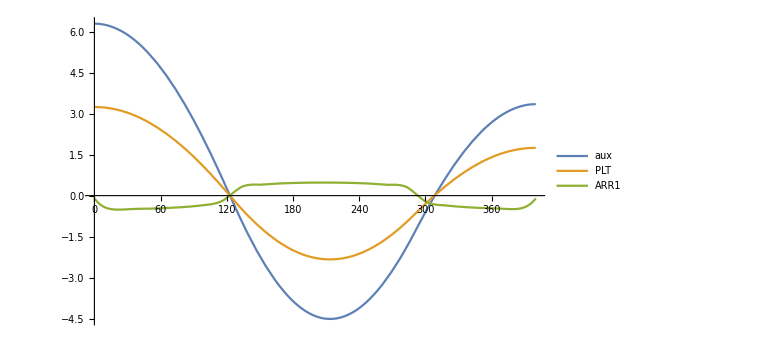

```mathematica
solveplotUnifLag= Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvUnifGrowth[[1]]/.t->tFinal],{X,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large]
```

```mathematica
Manipulate[ Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvUnifGrowth[[1]]],{X,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large],{t,0,tFinal}]
```

Part::partd: Part specification solLagAdvUnifGrowth⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {solLagAdvUnifGrowth⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
file1=Import["/Users/micolderuvo/Desktop/wt.png"]
```

-Graphics-

-Graphics-

```mathematica
%1751
```

%1751

```mathematica
file1=-Graphics-
```

-Graphics-

```mathematica
file2=Import["/Users/micolderuvo/Desktop/wt7.png"];
```

```mathematica
%1762
```

%1762

```mathematica
file2=-Graphics-
```

-Graphics-

```mathematica
images={file1,file1,file1,file1,file1,file1,file1,file1,file1,file1,file1,file1,file1,file1,file2,file2,file2,file2,file2,file2,file2};
```

```mathematica
Length[images]
```

21

```mathematica
Export["video.mov",images, "FrameRate"->3];
```

```mathematica
SystemOpen["video.mov"]
```

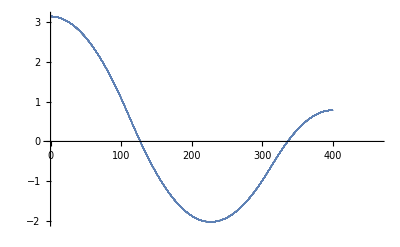
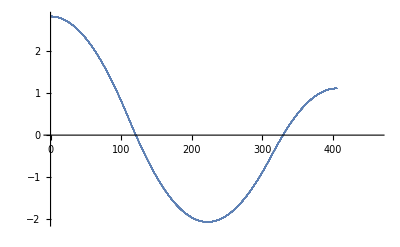
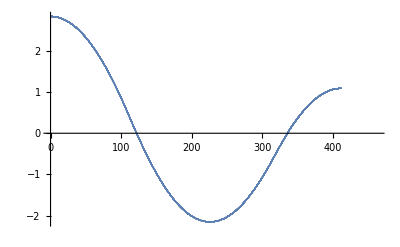
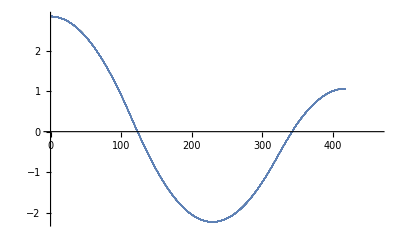
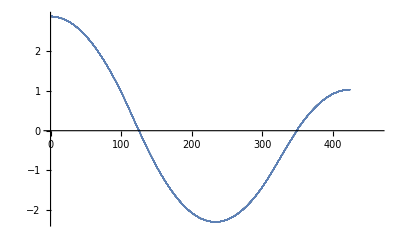
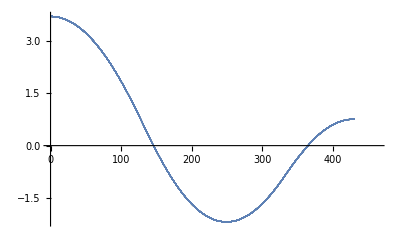
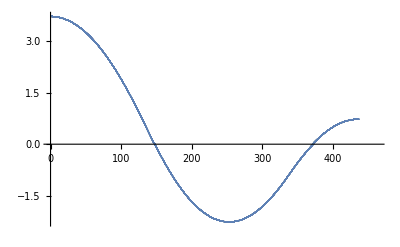
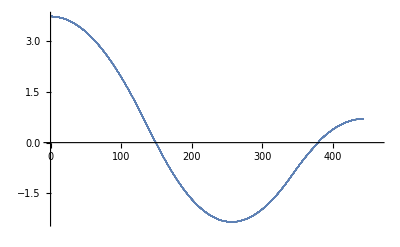

```mathematica
plotapproxPLTARRornull=Table[ListPlot[Table[Flatten@{ⅇ^(t (10^-8 ArcTan[Sin[0.3*Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15]/Exp[30*(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15)*0.2]]+10^-6)) X/.X->XVal/.t-> tVal,Evaluate[PLT[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,length,0.01}],PlotRange->{{0,ⅇ^(tFinal(10^-8 ArcTan[Sin[0.3*Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]-3.15]/Exp[30*(Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]-3.15)*0.2]]+10^-6)) length},All},PlotStyle->{PointSize[0.002]}],{tVal,0,tFinal,tFinal/10}]
```

```mathematica
(*plotonlyPLTorARR1=Table[ListPlot[Table[Flatten@{ⅇ^(t If[(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]>newPLTlimit &&PLTxmaxima[[1]]≤ X≤  auxinmin),growthPLT,If[Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]≤ 0,basalgrowth,10^-9]]) X/.X->XVal/.t-> tVal,Evaluate[PLT[XVal,tVal]/.solLagAdvUnifGrowthARR1⟦1⟧]},{XVal,0,length,0.01}],PlotRange->{{0,ⅇ^(tFinal*If[(Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]>newPLTlimit &&PLTxmaxima[[1]]≤ X≤  auxinmin),growthPLT,If[Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]≤ 0,basalgrowth,10^-9]])*length},All},PlotStyle->{PointSize[0.002]}],{tVal,0,tFinal,tFinal/10}]*)
```

```mathematica
ⅇ^(tFinal*If[Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]>2.5421709215989523&&2.623757072502947*^-6≤X≤226.82783857473885&&!112.48633183653722≤X≤ 312.5607413604466,10^-5,10^-4])*length
```

400 ⅇ^(5000 If[2.62376×10^-6≤X≤226.828&&!112.486≤X≤312.561,1/10^5,1/10^4])

```mathematica
Evaluate[PLT[4.9,2000]/.solLagAdvUnifGrowth⟦1⟧]
```

2.89412

```mathematica
Length[eulerian]
```

501

```mathematica
(*animationTableUnif=Table[Show[ListPlot[Table[Flatten@{XVal(1+(γonlyMZPLT*tVal)/.X->XVal/.t-> tVal),Evaluate[aux[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,length,0.1}],PlotStyle->Blue],ListPlot[Table[Flatten@{XVal(1+(γonlyMZPLT*tVal)/.X->XVal/.t-> tVal),Evaluate[ARR1[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,length,0.1}],PlotStyle->Green],ListPlot[Table[Flatten@{XVal(1+(γonlyMZPLT*tVal)/.X->XVal/.t-> tVal),Evaluate[PLT[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,length,0.1}],PlotStyle->Red],PlotRange-> {length*(1+(γonlyMZPLT*tFinal)/.X-> length./t-> Final),All}ImageSize->Large,Frame ->True,FrameLabel->{"Distance from QC [μm]","concentration [a.u.]"},RotateLabel->True,AxesLabel->StyleForm[" ",FontSize->20], BaseStyle->{FontSize->14}],{tVal,0,tFinal,1000}]*)
```

```mathematica
(*

animationTablenonUnifonlyPLTARR1=Table[Show[ListPlot[Table[Flatten@{ⅇ^(t If[(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]>newPLTlimit &&PLTxmaxima[[1]]≤ X≤  auxinmin),growthPLT,If[Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]<0,basalgrowth,0]]) X/.X->XVal/.t-> tVal,Evaluate[aux[XVal,tVal]/.solLagAdvUnifGrowthARR1⟦1⟧]},{XVal,0,length,0.01}],PlotStyle->Blue],ListPlot[Table[Flatten@{ⅇ^(t If[(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]>newPLTlimit &&PLTxmaxima[[1]]≤ X≤  auxinmin),growthPLT,If[Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]<0,basalgrowth,0]]) X/.X->XVal/.t-> tVal,Evaluate[ARR1[XVal,tVal]/.solLagAdvUnifGrowthARR1⟦1⟧]},{XVal,0,length,0.01}],PlotStyle->Green],ListPlot[Table[Flatten@{ⅇ^(t If[(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]>newPLTlimit &&PLTxmaxima[[1]]≤ X≤  auxinmin),growthPLT,If[Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]<0,basalgrowth,0]]) X/.X->XVal/.t-> tVal,Evaluate[PLT[XVal,tVal]/.solLagAdvUnifGrowthARR1⟦1⟧]},{XVal,0,length,0.01}],PlotStyle->Red],PlotRange->{{0,ⅇ^(tFinal If[(Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]>newPLTlimit &&PLTxmaxima[[1]]≤ X≤  auxinmin),growthPLT,If[Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]<0,basalgrowth,0]]) *length},All},ImageSize->Large,Frame ->True,FrameLabel->{"Distance from QC [μm]","concentration [a.u.]"},RotateLabel->True,AxesLabel->StyleForm[" ",FontSize->20], BaseStyle->{FontSize->14}],{tVal,0,tFinal,tFinal/10}]*)
```

```mathematica
(*animationTablenonUnif=Table[Show[ListPlot[Table[N[Flatten@{ ⅇ^(tVal*γonlyMZPLT/.X-> XVal/.t-> tVal) XVal,Evaluate[aux[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]}],{XVal,0,length,0.1},{tVal,0,tFinal,100}],PlotStyle->Blue,PlotRange->All],ListPlot[Table[N[Flatten@{ⅇ^(tVal*γonlyMZPLT/.X-> XVal/.t-> tVal) XVal,Evaluate[ARR1[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]}],{XVal,0,length,0.1},{tVal,0,tFinal,100}],PlotStyle->Green,PlotRange->All],ListPlot[Table[N[Flatten@{ⅇ^(tVal*γonlyMZPLT/.X-> XVal/.t-> tVal) XVal,Evaluate[PLT[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]}],{XVal,0,length,0.1},{tVal,0,tFinal,100}],PlotStyle->Red,PlotRange->All]],{tVal,0,tFinal,100}]*)
```

```mathematica
animationTablenonUnifapproxPLTARR1ornull=Table[Show[ListPlot[Table[Flatten@{ⅇ^(t (10^-8 ArcTan[Sin[0.3*Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15]/Exp[10*(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15)*0.9]]+10^-6)) X/.X->XVal/.t-> tVal,Evaluate[aux[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,length,0.01}],PlotStyle->Blue],ListPlot[Table[Flatten@{ⅇ^(t (10^-8 ArcTan[Sin[0.3*Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15]/Exp[10*(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15)*0.9]]+10^-6)) X/.X->XVal/.t-> tVal,Evaluate[ARR1[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,length,0.01}],PlotStyle->Green],ListPlot[Table[Flatten@{ⅇ^(t (10^-8 ArcTan[Sin[0.3*Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15]/Exp[10*(Evaluate[PLT[X,t]/.solLagAdvUnifGrowth⟦1⟧]-3.15)*0.9]]+10^-6)) X/.X->XVal/.t-> tVal,Evaluate[PLT[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,length,0.01}],PlotStyle->Red],PlotRange->{{0,ⅇ^(tFinal (10^-8 ArcTan[Sin[0.3*Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]-3.15]/Exp[10*(Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]-3.15)*0.9]]+10^-6)) length},{-6,10}},ImageSize->Large,Frame ->True,FrameLabel->{"Distance from QC [μm]","concentration [a.u.]"},RotateLabel->True,AxesLabel->StyleForm[" ",FontSize->20], BaseStyle->{FontSize->14}],{tVal,0,230000,23000}];
```

InterpolatingFunction::dmval: Input value {0.,46000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01,46000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### With the following command we can check how much has the domain grown:

```mathematica
ⅇ^(tFinal*If[And[Evaluate[PLT[length,tFinal]/.solLagAdvUnifGrowth⟦1⟧]>newPLTlimit,PLTxmaxima⟦1⟧≤ X≤ auxinmin] ,10^-6,10^-5])*length
```

400 √ⅇ

```mathematica
N[400 ⅇ^(3/10000)]
```

400.12

```mathematica
N[400 ⅇ^(1/50)]
```

408.081

```mathematica
(* animationTablePLT=Table[ListPlot[Table[Flatten@{XVal(1+(10^-5*tVal)/.X->XVal),Evaluate[PLT[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,400,0.1}],PlotRange->{{0,400(1+(10^-5*100000))},All},PlotStyle->{Red,PointSize[0.002]},Frame ->True,FrameLabel->{"Distance from QC [μm]","molecule concentration [a.u.]"},RotateLabel->True,AxesLabel->StyleForm[" ",FontSize->20], BaseStyle->{FontSize->14},ImageSize->Large],{tVal,0,100000,10000}];*)
```

```mathematica
(*animationTableARR1=Table[ListPlot[Table[Flatten@{XVal(1+(10^-5*tVal)/.X->XVal),Evaluate[ARR1[XVal,tVal]/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,400,0.1}],PlotRange->{{0,400(1+(10^-5*100000))},All},PlotStyle->{Green,PointSize[0.002]},Frame ->True,FrameLabel->{"Distance from QC [μm]","auxin concentration [pmol/μm]"},RotateLabel->True,AxesLabel->StyleForm[" ",FontSize->20], BaseStyle->{FontSize->14},ImageSize->Large],{tVal,0,100000,10000}];*)
```

```mathematica
(*Export["turing_growth_PLTARR1.avi",animationTablenonUnifonlyPLTARR1, "FrameRate"->3]
*)
```

```mathematica
Export["turing_growth_PLTARR1ornull.avi",animationTablenonUnifapproxPLTARR1ornull, "FrameRate"->3]
```

turing_growth_PLTARR1ornull.avi

```mathematica
(*SystemOpen["turing_growth_PLTARR1.avi"]
*)
```

```mathematica
SystemOpen["turing_growth_PLTARR1ornull.avi"]
```

```mathematica
(*Max[pltvalues]*)
```

```mathematica
(*Plot[Evaluate[{PLT[X,t]}/.solLagAdvUnifGrowth⟦1,2⟧/.t->10000],{X,0,NewLength},PlotRange-> {3.4,3.9},ImageSize-> Large, Epilog->{Red, Dashed,Line[{{0,3.6},{NewLength,3.6}}],AbsolutePointSize@5,Red,Point[{#,PLT[#,10000]/.solLagAdvUnifGrowth⟦1,2⟧}&/@(Table[imppos⟦i,2⟧,{i,1,Length[imppos]}])]}]
*)
```

```mathematica
(*Manipulate[Plot[Evaluate[{aux[X,t],PLT[X,t],ARR1[X,t]}/.solLagAdvUnifGrowth⟦1⟧],{X,0,NewLength},PlotRange->All,ImageSize->Large,PlotLabel->(*"t = "<>ToString[t]<>*)", γ= "<>ToString[Evaluate[γonlyMZPLT/. solLagAdvUnifGrowth⟦1⟧]]],{t,0,5000}]
*)
```

```mathematica
(**)
```

```mathematica
(**)
```

```mathematica
(*γonlyMZPLT/.solLagAdvUnifGrowth⟦1⟧/.t->1000/.X-> 55*)
```

```mathematica
(*turingrowth= Table[
ListPlot[Table[Flatten@{(ⅇ^(t If[PLT[X,t]>5.8346,0.0006-0.0006/(1+Exp[-X] 10^34),0]) X)/.X->XVal/.t-> tVal,Evaluate[{aux[XVal,tVal],PLT[XVal,tVal],ARR1[XVal,tVal]}/.solLagAdvUnifGrowth⟦1⟧]},{XVal,0,500,0.1}],PlotRange->{{0,(ⅇ^(t If[PLT[X,t]>5.8346,0.0006-0.0006/(1+Exp[-X] 10^34),0]))/.X->800/.t-> 1000}},PlotStyle->{PointSize[0.002]},Frame ->True,AxesLabel->StyleForm[" ",FontSize->20], BaseStyle->{FontSize->14},ImageSize->Large],{tVal,0,1000,50}];*)
```

```mathematica
(*Export["turingrowth.avi",turingrowth, "FrameRate"->10]
*)
```

```mathematica
(*SystemOpen["turingrowth.avi"]*)
```